```mathematica
FileNameSetter[Dynamic[filename]]
```

Browse…

```mathematica
data=Import[filename,"Data"];
```

```mathematica
bg=Import[DirectoryName[filename]<>"background.jpg"];
```

```mathematica
bg
```

-Graphics-

```mathematica
data[[1;;10]]//TableForm
```

0 | 480 | 0 | 0 | 0 | 0
288 | 263 | 0 | 0 | 90 | 1
295.534 | 258.556 | 17.4918 | 0.982683 | 148.392 | 8
242.743 | 214.855 | 16.496 | 142.762 | 129.6 | 13
309.789 | 245.44 | 149.715 | 441.32 | 155.749 | 28
309.222 | 245.211 | 149.92 | 441.237 | 155.376 | 34
252.759 | 216.516 | 34.1569 | 343.001 | 142.537 | 25
249.411 | 219.082 | 42.5948 | 343.001 | 142.537 | 22
266.119 | 264.068 | 73.1173 | 440.347 | 153.135 | 20
247.798 | 219.935 | 46.1925 | 342.393 | 142.537 | 19

```mathematica
trimdata=data[[1000;;-500]];
```

```mathematica
pos=data[[All,{1,2}]];
```

```mathematica
data[[{1,2},{1,2}]]
```

{{0,480},{288,263}}

```mathematica
Show[bg]
```

-Graphics-

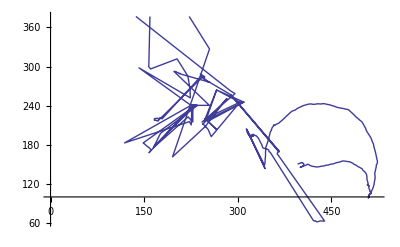

```mathematica
ListLinePlot[pos]
```

```mathematica
Show[Graphics[Raster[ImageData[ImageReflect[bg]]]],ListLinePlot[pos]]
```

-Graphics-

```mathematica
Manipulate[ListLinePlot[pos[[t;;t+d]]], {t,1,Length[pos],100}, {d,2,Length[pos],10}]
```

```mathematica
lengths =Map[Norm,Differences[trimdata]];
```

```mathematica
Max[lengths]
```

83.866

```mathematica
Dimensions[Transpose[trimdata[[1;;-2]]]]
```

{2,27888}

```mathematica
Dimensions[Transpose[{lengths}]]
```

{27888,1}

```mathematica
dataXYZ=Transpose[Append[Transpose[trimdata[[1;;-2]] ],lengths/Max[lengths]]] ;
```

```mathematica
ListPlot3D[dataXYZ,ColorFunction->Function[{x,y,z},Hue[z]]]
```

-Graphics3D-

```mathematica
Dimensions[dataXYZ]
```

{3,27888}

```mathematica
lengths
```

{2.80994,1.763,2.45459,2.35383,2.95897,1.48358,2.81257,«27874»,4.24462,3.91047,5.00927,3.12224,3.12145,2.06155,2.5}

```mathematica
Length[lengths]
```

29386

```mathematica
totalLength = Total[lengths]
```

67468.7